```mathematica
(*Get A,B,C,D coeficients from Eqs.(24,B1-B3) of 2106.10291*)
$Assumptions={y>0&&ν>0&&χ>0&&δμ>0&&δμ<1&&xx>0&&S1>0&&S2>0&&s1>0&&s2>0&&μ1>0&&μ2>0&&δχ>0&&s1z>0&&s2z>0&&s1p>0&&s2p>0&&α>0&&m>0&&m<1};
a0[J2_,L_,y_,χ_,δμ_,ν_,S1_,S2_]=1-y χ;
b0[J2_,L_,y_,χ_,δμ_,ν_,S1_,S2_]=(y (-2 ν(J2-L^2-L χ)+δμ(S1^2-S2^2)-δμ^2(2 L^2+S1^2+S2^2)))/(2 ν^2);
c0[J2_,L_,y_,χ_,δμ_,ν_,S1_,S2_]=y/(2 ν^2)((1+δμ^2)χ (S1^2-S2^2)+2 δμ(2L(J2-L^2-L χ)-(2 L +χ)(S1^2+S2^2)-ν L χ^2));
d0[J2_,L_,y_,χ_,δμ_,ν_,S1_,S2_]=1/(2 ν^2)y (-2 (J2-L^2-L χ) (J2-L^2-L χ-2 (S1^2+S2^2)-ν χ^2)+(S1^2-S2^2) (δμ χ^2-2 (S1^2-S2^2))-χ^2(S1^2+S2^2));
j2approx0[xx_,y_,ν_,S1_,S2_,S1z_,S2z_]=(ν/y)^2+2 ν/y(S1z + S2z)+S1^2+S2^2+2S1z S2z+ν xx;
j2approx[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[j2approx0[xx,y,(1-δμ^2)/4,((1+δμ)/2)s1,((1-δμ)/2)s2,((1+δμ)/2)s1z,((1-δμ)/2)s2z]];
aa[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[a0[j2approx[xx,y,δμ,s1z,s2z,s1,s2],(1-δμ^2)/(4y),y,s1z+s2z,δμ,(1-δμ^2)/4,((1+δμ)/2)s1,((1-δμ)/2)s2]]
bb[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[b0[j2approx[xx,y,δμ,s1z,s2z,s1,s2],(1-δμ^2)/(4y),y,s1z+s2z,δμ,(1-δμ^2)/4,((1+δμ)/2)s1,((1-δμ)/2)s2]]
cc[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[c0[j2approx[xx,y,δμ,s1z,s2z,s1,s2],(1-δμ^2)/(4y),y,s1z+s2z,δμ,(1-δμ^2)/4,((1+δμ)/2)s1,((1-δμ)/2)s2]]
dd[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[d0[j2approx[xx,y,δμ,s1z,s2z,s1,s2],(1-δμ^2)/(4y),y,s1z+s2z,δμ,(1-δμ^2)/4,((1+δμ)/2)s1,((1-δμ)/2)s2]]
```

1-y (s1z+s2z)

-((s1^2+s2^2+2 s1z s2z+xx) y)+(-s1z+s2z) δμ-δμ^2/y

2 (s1-s2) (s1+s2) (s1z+s2z) y-(s1z-s2z)^2 δμ+2 xx δμ+(2 (s1z-s2z) δμ^2)/y

-((s1z^2 s2^2-2 s1z^3 s2z+2 s1z s2^2 s2z+s2^2 s2z^2-2 s1z s2z^3+s1^2 (s1z-2 s2+s2z) (s1z+2 s2+s2z)-(s1z-s2z)^2 xx+xx^2) y)+(s1z-s2z) ((s1z-s2z)^2-2 xx) δμ-((s1z-s2z)^2 δμ^2)/y

```mathematica
FullSimplify[dd[xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,s1,s2 ]-(-(2 xx y+δχ (2 δμ-y δχ))^2/(4 y)+1/4(4 s1^2-χ^2)(4 s2^2-χ^2)y )]
```

0

```mathematica
(*Write stuff instead in terms of sp^2=s^2-sz^2*)
j2p[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_ ]=FullSimplify[j2approx[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2) ]];
bbp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=FullSimplify[bb[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2) ]]
ccp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=FullSimplify[cc[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2) ]]
ddp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=FullSimplify[dd[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2) ]]
```

-((s1p^2+s2p^2+(s1z+s2z)^2+xx) y)+(-s1z+s2z) δμ-δμ^2/y

2 (s1z+s2z) (s1p^2+s1z^2-s2p^2-s2z^2) y-(s1z-s2z)^2 δμ+2 xx δμ+(2 (s1z-s2z) δμ^2)/y

-((s1z^4+s2p^2 s2z^2+s2z^4+s1p^2 (-4 s2p^2+(s1z-s2z) (s1z+3 s2z))-s2z^2 xx+xx^2+2 s1z s2z (s2p^2+xx)-s1z^2 (3 s2p^2+2 s2z^2+xx)) y)+(s1z-s2z) ((s1z-s2z)^2-2 xx) δμ-((s1z-s2z)^2 δμ^2)/y

```mathematica
(*Compute p and q from Eqs.(29-30)*)
pp[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[Expand[1/y^2(bb[xx,y,δμ,s1z,s2z,s1,s2]^2/3-δμ cc[xx,y,δμ,s1z,s2z,s1,s2])]];
qq[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_ ]=FullSimplify[Expand[1/y^3((2 bb[xx,y,δμ,s1z,s2z,s1,s2]^3)/27-(δμ bb[xx,y,δμ,s1z,s2z,s1,s2] cc[xx,y,δμ,s1z,s2z,s1,s2])/3+δμ^2 dd[xx,y,δμ,s1z,s2z,s1,s2])]];
(*Compute the discriminant*)
discez[b_,c_,d_]=FullSimplify[Expand[(1/3(b^2/3-c))^3-(1/2((2 b^3)/27-(b c)/3+d))^2]]
disc[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_]=FullSimplify[Expand[discez[bb[xx,y,δμ,s1z,s2z,s1,s2 ],δμ cc[xx,y,δμ,s1z,s2z,s1,s2 ],δμ^2 dd[xx,y,δμ,s1z,s2z,s1,s2 ]]]];
```

1/108 (b^2 c^2-4 c^3-4 b^3 d+18 b c d-27 d^2)

```mathematica
(*Compute the p, q and discriminant in terms of the perpendicular spins*)
ppp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_ ]=FullSimplify[pp[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2)]];
qqp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_ ]=FullSimplify[qq[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2)]];
discsp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=FullSimplify[disc[xx,y,δμ,s1z,s2z,√(s1z^2+s1p^2),√(s2z^2+s2p^2)]];
```

```mathematica
discspseries[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=FullSimplify[Series[discsp[α^2 xx,y,δμ,s1z,s2z,α s1p,α s2p],{α,0,4}]];
FullSimplify[Expand[Normal[discspseries[xx,y,δμ,s1z,s2z,s1p,s2p]/α^4]-1/(27 y^2)4 δμ^2 (χ^2 y^2-2 δχ y δμ+δμ^2)^2 ((s1p^2+s2p^2+xx) (s1z^2 s2p^2+s1p^2 s2z^2-s1z s2z xx) y^2+((s2z s1p^2 - s1z s2p^2)xx-2 s1p^2 s2p^2 δχ) y δμ+s1p^2 s2p^2 δμ^2)]/.{χ->s1z+s2z,δχ->s1z-s2z}]
```

0

```mathematica
(*We want to show that p is always grater than 0*)
ppp2[xx_,z_,χ_,δχ_,sp1_,sp2_]=FullSimplify[ppp[xx,y,y z,(χ+δχ)/2,(χ-δχ)/2,s1p,s2p ]]
(*We can see p as a parabola in δχ with a>0*)
SeriesCoefficient[ppp2[xx,z,χ,δχ,sp1,sp2],{δχ,0,2}]
(*We compute its discriminant, if it is smaller than 0, there are no real roots and p>0 always*)
pdiscδχ[xx_,z_,χ_,sp1_,sp2_]=FullSimplify[SeriesCoefficient[ppp2[xx,z,χ,δχ,sp1,sp2],{δχ,0,1}]^2-4 SeriesCoefficient[ppp2[xx,z,χ,δχ,sp1,sp2],{δχ,0,2}] SeriesCoefficient[ppp2[xx,z,χ,δχ,sp1,sp2],{δχ,0,0}]]
(*This discriminant is a parabola in z with a<0*)
FullSimplify[SeriesCoefficient[pdiscδχ[xx,z,χ,sp1,sp2]/z^2,{z,0,2}]]
(*Since the discriminant of this parabola is always negative, it has no real roots and all values are negative -> p>0*)
pdiscδχz[xx_,χ_,sp1_,sp2_]=FullSimplify[SeriesCoefficient[pdiscδχ[xx,z,χ,sp1,sp2]/z^2,{z,0,1}]^2-4 SeriesCoefficient[pdiscδχ[xx,z,χ,sp1,sp2]/z^2,{z,0,2}] SeriesCoefficient[pdiscδχ[xx,z,χ,sp1,sp2]/z^2,{z,0,0}]]
```

1/3 (s1p^4+s2p^4+xx^2-4 xx z^2+z^4+2 xx z δχ-4 z^3 δχ+4 z^2 δχ^2+2 (xx+z^2-2 z δχ) χ^2+χ^4+2 s1p^2 (s2p^2+xx+z (z+δχ)-3 z χ+χ^2)+2 s2p^2 (xx+z (z+δχ)+3 z χ+χ^2))

(4 z^2)/3

-4/3 z^2 (s1p^4+s2p^4+2 s1p^2 (s2p^2+xx+2 (z-χ)^2)+xx (xx-4 z^2+4 χ^2)+2 s2p^2 (xx+2 (z+χ)^2))

-16/3 (s1p^2+s2p^2-xx)

256/9 (-((s1p^2+s2p^2-xx) (s1p^2+s2p^2+xx)^2)+4 (-4 s1p^2 s2p^2+xx^2) χ^2)

```mathematica
(*Compute B, C, D in terms of perpendicular spin*)
FullSimplify[Series[bbp[α^2 xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,α s1p,α s2p],{α,0,10}]]
FullSimplify[Series[ccp[α^2 xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,α s1p,α s2p],{α,0,10}]]
FullSimplify[Series[ddp[α^2 xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,α s1p,α s2p],{α,0,10}]]
```

(-(δμ (δμ+y δχ))/y-y χ^2)-(s1p^2+s2p^2+xx) y α^2+O[α]^11

δχ ((2 δμ^2)/y-δμ δχ+2 y χ^2)+(2 xx δμ+2 (s1p-s2p) (s1p+s2p) y χ) α^2+O[α]^11

-(δχ^2 (δμ^2-y δμ δχ+y^2 χ^2))/y+(-2 xx δμ δχ+y δχ (xx δχ+s1p^2 (δχ-2 χ)+s2p^2 (δχ+2 χ))) α^2+(4 s1p^2 s2p^2-xx^2) y α^4+O[α]^11

```mathematica
(*Writte the constants B, C and D in simpler terms*)
transform={j2a->δμ^2/y+y χ^2,δΧ->δμ δχ,bp ->y(s1p^2+s2p^2+xx),cp->-2δμ( xx δμ+(s1p^2-s2p^2) y χ), dp->δμ^2(4 s1p^2 s2p^2-xx^2) y};
bbs:=-j2a-δΧ-bp ;
δμccs:=δΧ (2j2a -δΧ)-cp;
δμ2dds:=-δΧ^2 (j2a -δΧ)+(δΧ^2 bp+δΧ cp)+dp;
FullSimplify[(bbs/.transform)-bbp[ xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,s1p,s2p]]
FullSimplify[(δμccs/.transform)-δμ ccp[ xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,s1p,s2p]]
FullSimplify[(δμ2dds/.transform)-δμ^2 ddp[ xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,s1p,s2p]]
discs=FullSimplify[Expand[discez[bbs,δμccs,δμ2dds]]]
FullSimplify[Series[discs,{dp,0,10}]]
```

0

0

0

1/108 (4 cp^3+dp (-27 dp+4 (j2a-2 δΧ)^3)+18 cp dp (j2a-2 δΧ)+cp^2 (j2a-2 δΧ)^2+4 bp^4 δΧ^2+bp^2 (cp^2+4 (j2a-2 δΧ)^2 δΧ^2+12 dp (j2a+δΧ)+8 cp δΧ (j2a+4 δΧ))+2 bp (6 dp (j2a-2 δΧ) (j2a+δΧ)+cp^2 (j2a+10 δΧ)+cp (9 dp+2 (j2a-2 δΧ)^2 δΧ))+4 bp^3 (dp+δΧ (cp+2 δΧ (j2a+2 δΧ))))

1/108 (cp+2 bp δΧ)^2 (bp^2+4 cp+(j2a-2 δΧ)^2+2 bp (j2a+2 δΧ))+1/54 (bp+j2a-2 δΧ) (9 cp+2 (bp^2+(j2a-2 δΧ)^2+bp (2 j2a+5 δΧ))) dp-dp^2/4+O[dp]^11

```mathematica
(*Compute p and q from in terms of these simpler terms*)
transform2={pal->(j2a-2 δΧ+bp)/3, pperp->cp/2+ bp δΧ};
pps:=3 pal^2+2pperp;
qqs:=-2pal(pal^2+ pperp) +dp;
FullSimplify[Expand[(pps/.transform2/.transform) - y^2 pp[xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,√(((χ+δχ)/2)^2+s1p^2),√(((χ-δχ)/2)^2+s2p^2) ]]]
FullSimplify[Expand[(qqs/.transform2)-((2 bbs^3)/27-(bbs δμccs)/3+δμ2dds)]]
(*Compute the discriminant in terms of these variables*)
discss=FullSimplify[Expand[(pps/3)^3-(qqs/2)^2]]
```

0

0

-dp^2/4+dp pal (pal^2+pperp)+1/27 pperp^2 (9 pal^2+8 pperp)

```mathematica
FullSimplify[bbs^2/3-δμccs-(1/3(j2a-2 δΧ+bp)^2+cp+2 bp δΧ)]
```

0

```mathematica
(*Define sum of moduli of perpendicular part of spins*)
Sperp2func[S1_,S1z_]=S1^2-S1z^2;
(*Find perpendicular part of angular momentum*)
j2perpfunc[xx_,S1_,S2_,S1z_,S2z_]=FullSimplify[j2approx0[xx,y,ν,S1,S2,S1z,S2z]-(ν/y+S1z+S2z)^2];
FullSimplify[j2perpfunc[xx,S1,S2,S1z,S2z]-(Sperp2func[S1,S1z]+Sperp2func[S2,S2z]+ ν xx)]
(*Define parallel total angular momentum J\dotLhat*)
jparallel[L_,δμ_,χ_,δχ_]=L+1/2(χ+δμ δχ);
FullSimplify[jparallel[L,δμ,s1z+s2z,s1z-s2z]-(L+(1+δμ)/2 s1z+(1-δμ)/2 s2z)]
```

0

0

```mathematica
(*Series for J \pm Jparallel*)
FullSimplify[Series[√(l^2(1+2x))-l,{x,0,4}],Assumptions->l>0]
FullSimplify[Series[√(l^2(1+2x))+l,{x,0,4}],Assumptions->l<0]
```

l x-(l x^2)/2+(l x^3)/2-(5 l x^4)/8+O[x]^5

-l x+(l x^2)/2-(l x^3)/2+(5 l x^4)/8+O[x]^5

```mathematica
(*Compute N-,B-,C- from Eq.(26,41-46)*)
nm0[J_,L_,ν_,χ_,δμ_, S1_,S2_]=(J-L)(J-L-2ν χ)-δμ (S1^2-S2^2);
bm0[J_,L_,χ_,δμ_,δχav_]=2(J-L)-χ-δμ δχav;
cm0[δμ_,δχdiff_]=-δμ δχdiff;
FullSimplify[jparallel[L,δμ,s1z+s2z,s1z-s2z]-(L+(1+δμ)/2 s1z+(1-δμ)/2 s2z)]
FullSimplify[bm0[J,L,χ,δμ,δχ]-2(J -jparallel[L,δμ,χ,δχ])]
FullSimplify[Expand[nm0[jparallel[L,δμ,χ,δχ],L,(1-δμ^2)/4,χ,δμ, S1,S2]]/.{χ->s1z+s2z,δχ->s1z-s2z}/.{s1z->2/(1+δμ)S1z,s2z->2/(1-δμ)S2z }];
FullSimplify[Solve[{nm0[J,L,(1-δμ^2)/4,χ,δμ, S1,S2]+δμ (S1^2-S2^2-1/4(δμ δχ+χ) (δχ+δμ χ))==0},J]];
FullSimplify[(nm0[J,L,(1-δμ^2)/4,χ,δμ, S1,S2]-((J -jparallel[L,δμ,χ,δχ])(J -jparallel[L,δμ,χ,δχ]+2(μ1 S1z + μ2 S2z))-δμ (Sperp2func[S1,S1z]-Sperp2func[S2,S2z])))/.{χ->s1z+s2z,δχ->s1z-s2z}/.{s1z->1/μ1 S1z,s2z->1/μ2 S2z }/.{μ1->(1+δμ)/2,μ2->(1-δμ)/2}]
```

0

0

0

```mathematica
(*Compute N+,B+,C+ from Eq.(26,41-46)*)
np0[J_,L_,ν_,χ_,δμ_, S1_,S2_]=(J+L)(J+L+2ν χ)-δμ (S1^2-S2^2);
bp0[J_,L_,χ_,δμ_,δχav_]=2(J+L)+χ+δμ δχav;
cp0[δμ_,δχdiff_]=δμ δχdiff;
FullSimplify[bp0[J,L,χ,δμ,δχ]-2(J +jparallel[L,δμ,χ,δχ])]
FullSimplify[Expand[np0[-jparallel[L,δμ,χ,δχ],L,(1-δμ^2)/4,χ,δμ, S1,S2]]/.{χ->s1z+s2z,δχ->s1z-s2z}/.{s1z->2/(1+δμ)S1z,s2z->2/(1-δμ)S2z }];
FullSimplify[Solve[{np0[J,L,(1-δμ^2)/4,χ,δμ, S1,S2]+δμ (S1^2-S2^2-1/4(δμ δχ+χ) (δχ+δμ χ))==0},J]];
FullSimplify[(np0[J,L,(1-δμ^2)/4,χ,δμ, S1,S2]-((J +jparallel[L,δμ,χ,δχ])(J +jparallel[L,δμ,χ,δχ]-2(μ1 S1z + μ2 S2z))-δμ (Sperp2func[S1,S1z]-Sperp2func[S2,S2z])))/.{χ->s1z+s2z,δχ->s1z-s2z}/.{s1z->1/μ1 S1z,s2z->1/μ2 S2z }/.{μ1->(1+δμ)/2,μ2->(1-δμ)/2}]
```

0

0

```mathematica
(*Check the different combinations of N+, N-*)
FullSimplify[np0[J,L,ν,χ,δμ, S1,S2]+nm0[J,L,ν,χ,δμ, S1,S2]]
FullSimplify[np0[J,L,ν,χ,δμ, S1,S2]-nm0[J,L,ν,χ,δμ, S1,S2]]
```

2 (J^2+L^2+(-S1^2+S2^2) δμ+2 L ν χ)

4 J (L+ν χ)

```mathematica
(*Check how N-,B-,C- behave for small perpendicular spin*)
nmp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_ ]=FullSimplify[(nm0[Sqrt[j2p[xx,y,δμ,s1z,s2z,s1p,s2p ]],L,ν,χ,δμ, S1,S2]/.{L->ν/y, S1->μ1 √(s1p^2+s1z^2), S2->μ2 √(s2p^2+s2z^2),χ->s1z+s2z}/.{μ1->(1+δμ)/2, μ2->(1-δμ)/2,ν->(1-δμ^2)/4})];
FullSimplify[Series[nmp[α^2 xx,y,δμ,s1z,s2z,α s1p,α s2p],{α,0,2}]]
argG[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=ArcTan[-qqp[xx,y,δμ,s1z,s2z,s1p,s2p]/2,(√discsp[xx,y,δμ,s1z,s2z,s1p,s2p])/y^6];
δχavp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=y/δμ(-√(ppp[xx,y,δμ,s1z,s2z,s1p,s2p]/3)Cos[argG[xx,y,δμ,s1z,s2z,s1p,s2p]/3]-bbp[xx,y,δμ,s1z,s2z,s1p,s2p]/(3 y));
δχdiffp[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=y/δμ(√ppp[xx,y,δμ,s1z,s2z,s1p,s2p] Sin[argG[xx,y,δμ,s1z,s2z,s1p,s2p]/3]);
bm2mcm2[xx_,y_,δμ_,s1z_,s2z_,s1p_,s2p_]=Simplify[((bm0[Sqrt[j2p[xx,y,δμ,s1z,s2z,s1p,s2p ]],L,χ,δμ,δχavp[xx,y,δμ,s1z,s2z,s1p,s2p]])^2-(cm0[δμ,δχdiffp[xx,y,δμ,s1z,s2z,s1p,s2p]])^2)/.{L->ν/y, S1->μ1 √(s1p^2+s1z^2), S2->μ2 √(s2p^2+s2z^2),χ->s1z+s2z}/.{μ1->(1+δμ)/2, μ2->(1-δμ)/2,ν->(1-δμ^2)/4}];
FullSimplify[Series[bm2mcm2[α^2 xx,y,δμ,s1z,s2z,α s1p,α s2p],{α,0,2}]]
```

1/4 (δμ (s2p^2 (-1+δμ)^2-s1p^2 (1+δμ)^2)-(y (xx+s2p^2 (-1+δμ)^2-xx δμ^2+s1p^2 (1+δμ)^2) (s2z (-1+δμ)^2+s1z (1+δμ)^2))/(-2 s1z y (1+δμ)+(-1+δμ) (1+2 s2z y+δμ))) α^2+O[α]^3

O[α]^4

```mathematica
FullSimplify[Series[δχavp[xx,y,δμ,(χ+δχ)/2,(χ-δχ)/2,s1p,s2p],{δμ,0,0}]]
FullSimplify[Series[δχdiffp[xx,y,δμ,s1z,s2z,s1p,s2p],{δμ,0,0}]]
```

(χ (s1p^2-s2p^2+δχ χ))/(s1p^2+s2p^2+xx+χ^2)+O[δμ]^1

(√((s1p^2+s2p^2+xx) (4 s1z^2 s2p^2+4 s1p^2 (s2p^2+s2z^2)-4 s1z s2z xx-xx^2)))/((s1p^2+s2p^2+(s1z+s2z)^2+xx) y^3)+O[δμ]^1

```mathematica
(*Simplify also Subscript[(σ^(1)), 0] from Eq.(71)*)
sigmaprecavg01[J2_,L_,s1_,s2_,ν_,χ_,δμ_,μ1_,μ2_, δχ_]=1/ν(J2 -L^2-δμ(μ1 s1^2-μ2 s2^2)-L(χ+δμ δχ));
sigmaprecavg01ez[xx_,y_,δμ_,s1z_,s2z_,s1_,s2_,δχ_ ]=FullSimplify[sigmaprecavg01[j2approx[xx,y,δμ,s1z,s2z,s1,s2 ],(1-δμ^2)/(4y),s1,s2,(1-δμ^2)/4,s1z+s2z,δμ,(1+δμ)/2,(1-δμ)/2,δχ]];
FullSimplify[sigmaprecavg01ez[xx,y,δμ,s1z,s2z,s1,s2,δχ]-((s1^2+s2^2+2s1z s2z)+xx+δμ(s1z-s2z-δχ)/y)]
```

0

```mathematica
(*Compare the β from Antoine (Eq.B3a and C2c of 1801.08542) and TaylorF2 (Eq.6.23 of 0810.5336)*)
βAnt[μ1_,μ2_,s1z_,s2z_]=-(904/15 μ1+40 μ2)s1z -(40 μ1+904/15 μ2) s2z;
βF2[χs_,χa_,ν_,δμ_]=(113/12-19/3 ν)χs + 113/12 δμ χa;
FullSimplify[βF2[(χ1z+χ2z)/2,(χ1z-χ2z)/2,(1-δμ^2)/4,δμ]/βAnt[(1+δμ)/2,(1-δμ)/2,((1+δμ)/2)χ1z,((1-δμ)/2)χ2z]]
FullSimplify[-15/752 βAnt[(1+δμ)/2,(1-δμ)/2,(χ+δχ)/2,(χ-δχ)/2]]
```

-5/32

(19 δμ δχ)/94+χ

O[m]^3

O[m]^6

(-m/16+m^2/16-(71 m^3)/6144)/(1-(3 m)/2+(59 m^2)/96-(11 m^3)/192)

m^2/(1024 (1-m+(3 m^2)/32-(133 m^4)/32768-(133 m^5)/32768))

0

0

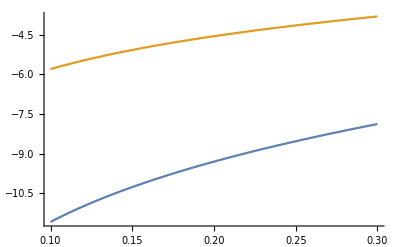

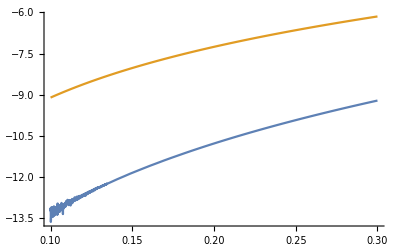

```mathematica
(*Explore simplifications of the Elliptic function coefficients for m<<1*)
ellipticfunc1[m_]=1/m (EllipticE[m]/EllipticK[m]-1+m/2);
ellipticfunc2[m_]=1/m^2 (EllipticE[m]^2/EllipticK[m]^2+(2 EllipticE[m])/(3 EllipticK[m])(m-2)+m^2/8-m/3+1/3);
s1[m_]=-m/16(1+m/2+41/128 m^2);
s2[m_]=m^2/1024(1+m+29/32 m^2+13/16 m^3);
Series[ellipticfunc1[m]-s1[m],{m,0,2}]
Series[ellipticfunc2[m]-s2[m],{m,0,5}]
p1[m_]=PadeApproximant[ellipticfunc1[m],{m,0,{3,3}}]
p2[m_]=PadeApproximant[ellipticfunc2[m],{m,0,{2,5}}]
FullSimplify[p1[m]-(-m(1-m+71/384 m^2)/(16-24m+59/6 m^2-11/12 m^3))]
FullSimplify[p2[m]-(m^2/(1024 - 1024 m +96 m^2-133/32 m^4(1+m)))]

Manipulate[{{N[Abs[ellipticfunc1[m]-p1[m]]],N[Abs[(ellipticfunc1[m]-p1[m])/ellipticfunc1[m]]]},{N[Abs[ellipticfunc2[m]-p2[m]]],N[Abs[(ellipticfunc2[m]-p2[m])/ellipticfunc2[m]]]}},{m,0.01,1}]

Plot[{Log10[Abs[ellipticfunc1[m]-p1[m]]],Log10[Abs[ellipticfunc1[m]-s1[m]]]},{m,0.1,0.3}]
Plot[{Log10[ellipticfunc2[m]-p2[m]],Log10[ellipticfunc2[m]-s2[m]]},{m,0.1,0.3}]
```

```mathematica
(*Explore simplifications of the Elliptic function coefficients for m->1*)
Series[EllipticE[m],{m,1,0}]
Series[EllipticK[m],{m,1,0}]
```

1+O[m-1]^1

1/2 (4 Log[2]-Log[1-m])+O[m-1]^1